### Atomic inversion W(t) for coherent states

```mathematica
W[t_,nb_,nmax_:100]:= ⅇ^-nb Total@Table[nb^n/(n!)Cos[2 t √(n+1)],{n,0,nmax}];
```

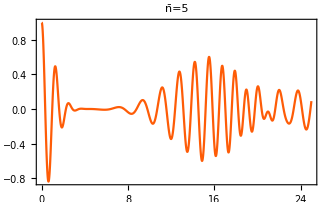

```mathematica
w = W[t,5,200];
plt1=Plot[w,{t,0,25},
PlotLabel->"n̄=5",
PlotStyle->COLORLIST[[2]]
]
```

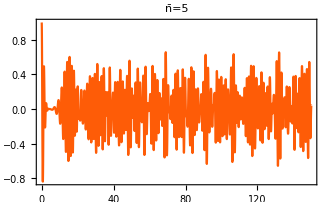

```mathematica
w = W[t,5,200];
plt2=Plot[w,{t,0,150},PlotPoints->100,
PlotLabel->"n̄=5",
PlotStyle->COLORLIST[[2]]
]
```

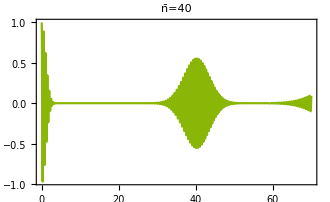

```mathematica
w = W[t,40,200];
plt3=Plot[w,{t,0,70},PlotPoints->100,
PlotLabel->"n̄=40",
PlotStyle->COLORLIST[[3]]
]
```

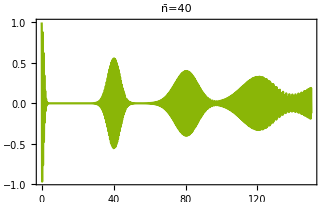

```mathematica
w = W[t,40,200];
plt4=Plot[w,{t,0,150},PlotPoints->100,
PlotLabel->"n̄=40",
PlotStyle->COLORLIST[[3]]
]
```

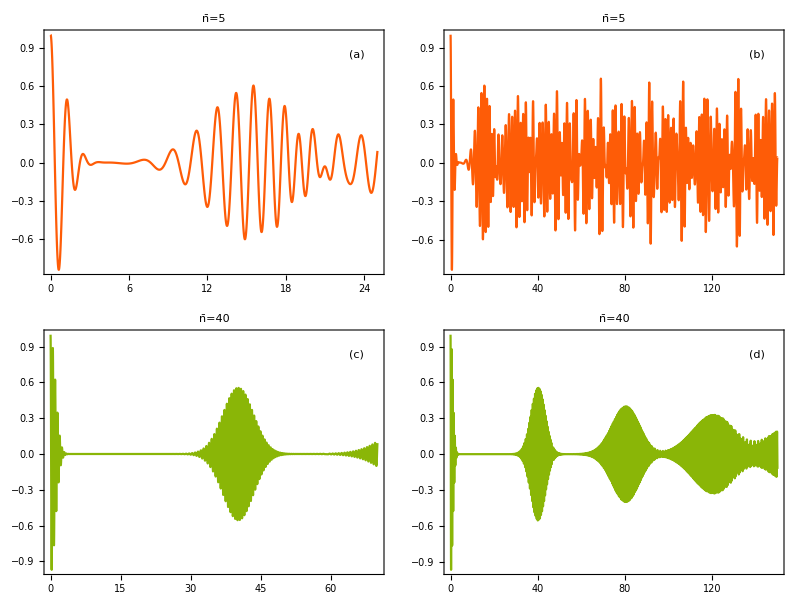

```mathematica
grid[{plt1,plt2,plt3,plt4},2]
```

```mathematica
9
```